# Elliptical dipole field wavefronts

This script calculates analytical expressions for and plots the wavefronts of an elliptical dipole field. An elliptical field is the superposition of angular momentum eigenstates, and exhibits supermomentum that can be measured by the displacement of the field image. Analogous figures for superimposed plane waves and point sources with supermomentum are published in M. Berry "Optical currents" (2009) Fig. 3

```mathematica
SetDirectory[NotebookDirectory[]];
$Assumptions={Element[{θ, ϕ, ρ, r, a,b,c, α, z,R, ρLim},Reals], ρ>0, r>0,a>0, n>=0, α≥0, α≤ 2, ϕ≥0, ϕ ≤  π, R≥ 0, ρLim>0, ρ<=1, ρLim<1};
```

## Coordinate system

## Define rotations and projection operator

```mathematica
Clear[Rx,Ry,Rz]
(*rotations in linear polarization basis*)
Rx[θ_] := {{1,0,0},{0 ,Cos[θ], Sin[θ]},{0, -Sin[θ], Cos[θ]}};
Ry[θ_] := {{Cos[θ],0,-Sin[θ]},{0, 1, 0},{Sin[θ], 0, Cos[θ]}};
Rz[θ_] := {{Cos[θ],Sin[θ],0},{-Sin[θ] ,Cos[θ],0},{0,0,1}};

(*V converts to circular basis*)
V=Sqrt[1/2]{{1,1,0},{I,-I,0},{0,0,Sqrt[2]}};
Vdag=ConjugateTranspose[V];

(*Projection operator*)
P = DiagonalMatrix[{1,1,0}];

(* 3D Rotation operator in linear basis *) 
U = Rz[-θ].Ry[-ϕ].Rz[θ];
Udag= ConjugateTranspose[U];

(* 3D Rotation operator in circular basis *) 
Uc = Vdag.U.V;
Ucdag = ConjugateTranspose[Uc];
```

## Calculate field

```mathematica
(* lab frame, linear basis greens function *)
G = FullSimplify[U.P.Udag]

(* dipole -  we set a value of α here but treat it generally again below *)
dip = {0,Cos[α*Pi],I Sin[α*Pi]};
(* field in yz plane *)
Eplane = FullSimplify[Exp[I k r]G.dip/.{k->1, θ->Pi/2}];
```

{{1/4 (3-Cos[2 θ]+2 Cos[θ]^2 Cos[2 ϕ]),-Cos[θ] Sin[θ] Sin[ϕ]^2,-Cos[θ] Cos[ϕ] Sin[ϕ]},{-Cos[θ] Sin[θ] Sin[ϕ]^2,1/4 (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2),-Cos[ϕ] Sin[θ] Sin[ϕ]},{-Cos[θ] Cos[ϕ] Sin[ϕ],-Cos[ϕ] Sin[θ] Sin[ϕ],Sin[ϕ]^2}}

```mathematica
(* coordinate transform *)
cotrans = {r->Sqrt[y^2+z^2], ϕ->ArcTan[z/y]};
MatrixForm[FullSimplify[Eplane//.cotrans]]
```

(0
(ⅇ^(ⅈ √(y^2+z^2)) y (y Cos[π α]-ⅈ z Sin[π α]))/(y^2+z^2)
(ⅇ^(ⅈ √(y^2+z^2)) z (-y Cos[π α]+ⅈ z Sin[π α]))/(y^2+z^2))

```mathematica
FullSimplify[Eplane[[2]]]
```

ⅇ^(ⅈ r) Cos[ϕ] (Cos[π α] Cos[ϕ]-ⅈ Sin[π α] Sin[ϕ])

## Plot with density plot - quick and dirty

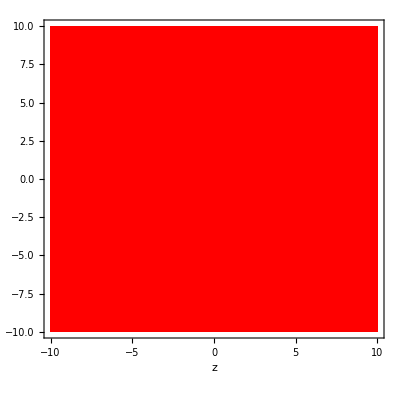

```mathematica
(* density plot based wavefront plot, colour where argument of field is 0 *)
cofunc[x_] := Hue[1,1,1,Piecewise[{{1,Abs[x]<0.03}}, 0]]

p1 =DensityPlot[Pi  Boole[y ≥ 0] + Arg[Eplane[[2]]//.cotrans/.α->0.4], {y,-10,10},{z, -10,10}, PlotPoints->100, ColorFunction->cofunc, ColorFunctionScaling->False, Axes->True, FrameLabel->{"z","", "", "y"}]
```

```mathematica
(* I've added a corrective pi phase shift on crossing the y axis, this shunts the discontinuity into the polarization. Without the shift we have *)

p1 =DensityPlot[ Arg[Eplane[[2]]//.cotrans/.α-> 0.4], {y,-10,10},{z, -10,10}, PlotPoints->100, ColorFunction->cofunc, ColorFunctionScaling->False, Axes->True,FrameLabel->{"z","", "", "y"}]
```

-Graphics-

## Analytic expression for the phase

```mathematica
(* Y polarized field component has the general form *)
EAn1 =  A Exp[I r](1 + a Cos[2ϕ] - I b Sin[2 ϕ]);
(* we can neglect the overall amplitude because we're interested in the phase. Then expanding gives us *)
EAn2=(Cos[r] + I Sin[r])(1 + a Cos[2ϕ] - I b Sin[2ϕ]);
(* In the space of elliptical dipoles we use in the Araneda 2018 and in my thesis a = 1 and b = ϵ = Tan[α] *)
```

```mathematica
(* we can expand this into real and imaginary parts *)
ER =  Cos[r] + a Cos[r]Cos[2ϕ] + b Sin[r]Sin[2ϕ];
EI =  Sin[r] + a Sin[r]Cos[2ϕ] - b Cos[r] Sin[2 ϕ];

(* the phase is arctan the real over imaginary part *)
Ephase = FullSimplify[ArcTan[ER/EI]];

(* the phase is zero when EI=0 *)
sol = Solve[EI == 0, {r}];

(* with a discontinuity when ER=0 *)
disc = Solve[(ER/.r->1) == 0, {ϕ}];

(* we can write the analytic solution *)
Clear[ϕ]
rsol =   Max[ ArcTan[b Sin[2 ϕ],(1+a Cos[2 ϕ])]+ 2 π C[1],0]
```

Max[0,ArcTan[b Sin[2 ϕ],1+a Cos[2 ϕ]]+2 π C[1]]

## Sigma+ dipole

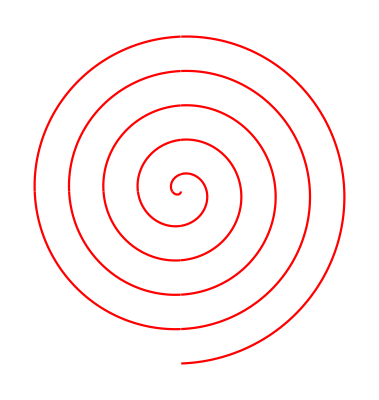

```mathematica
(* values to plot, α = 0.25 π, ϵ = 1 *)
vals = {a->1, b->1};

(* Plot other terms together *)
ap0 = Show[Table[PolarPlot[Pi Boole[Cos[ϕ]≥  0]+rsol/.vals/. C[1]->d, {ϕ, -Pi, Pi}, Exclusions->{ϕ==Pi/2, ϕ ==  -Pi/2}, PlotStyle->Red], {d, 0,4}]];

Show[ap0, Axes->False]
Export["Sigmap.pdf",%];
```

## Sigma- dipole

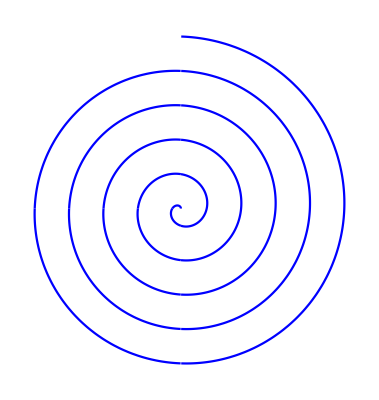

```mathematica
(* values to plot, α = 0.75 π, ϵ = -1 *)
vals = {a->1, b->-1};

(* Plot other terms together *)
ap1 = Show[Table[PolarPlot[Pi Boole[Cos[ϕ]≥  0]+rsol/.vals/. C[1]->d, {ϕ, -Pi, Pi}, Exclusions->{ϕ==Pi/2, ϕ ==  -Pi/2}, PlotStyle->Blue], {d, 0,4}]];

Show[ap1, Axes->False]
Export["Sigmam.pdf",%];
```

## Y dipole

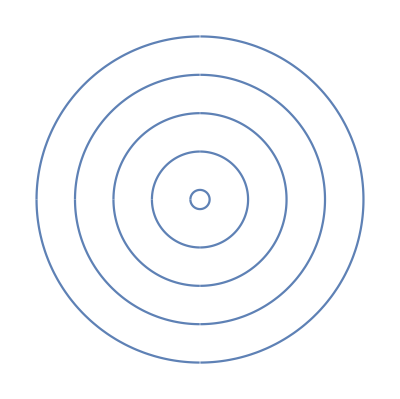

```mathematica
(* values to plot, α = 0, ϵ = 0 *)
vals = {a->1, b->0};

(* Plot other terms together *)
ap = Show[Table[PolarPlot[rsol/.vals/. C[1]->d, {ϕ, -Pi, Pi}, Exclusions->{ϕ==Pi/2, ϕ ==  -Pi/2}], {d, 0,4}]];

Show[ap, Axes->False]
```

## Z dipole

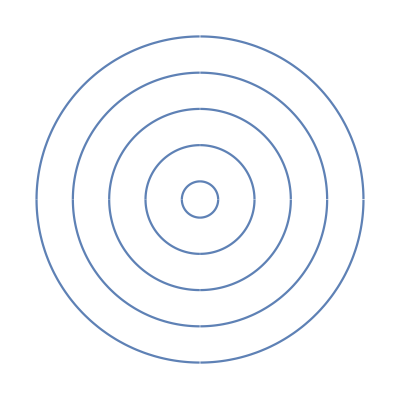

```mathematica
(* values to plot, α = 0.5 π, ϵ = Infinity *)
(* here we just approximate b->Infinity *)
vals = {a->1, b->10^100};

(* Plot other terms together *)
ap = Show[Table[PolarPlot[Pi Boole[Cos[ϕ]Sin[ϕ]≥  0]+rsol/.vals/. C[1]->d, {ϕ, -Pi, Pi}, Exclusions->{ϕ==Pi/2, ϕ ==  -Pi/2, ϕ==0}], {d, 0,4}]];

(* the z component is π out of phase with the y component *)
Show[ap, Axes->False]
```

## Maximally displaced dipole at NA=0.4

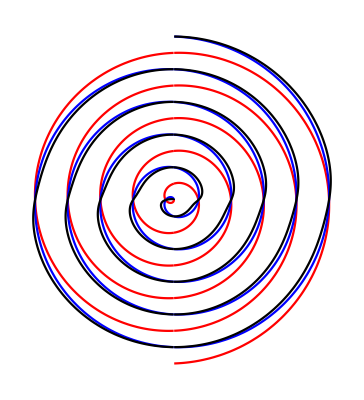

```mathematica
(* values to plot, α = 0.43 π, ϵ = 0 *)
vals = {a->1, b->-5};

(* Plot other terms together *)
ap2 = Show[Table[PolarPlot[Pi Boole[Cos[ϕ]≥  0]+rsol/.vals/. C[1]->d, {ϕ, -Pi, Pi}, Exclusions->{ϕ==Pi/2, ϕ ==  -Pi/2}, PlotStyle->Black], {d, 0,4}]];

Show[ap0, ap1,ap2, Axes->False]
Export["Elliptical.pdf",%];
```

## Linear and circular basis coefficients as function of α = arctan[ϵ]

```mathematica
N@Vdag.{Cos[α],I Sin[α],0}/.α->ArcTan[-5]
```

{-0.5547+0. ⅈ,0.83205+0. ⅈ,0.+0. ⅈ}

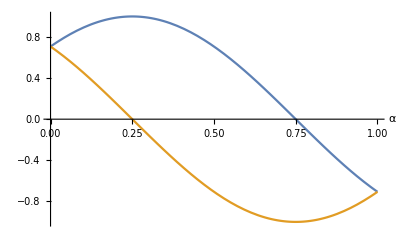

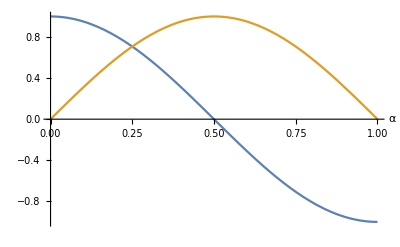

```mathematica
(* Circular basis components (in phase) *)
Plot[{Cos[Pi α]/(√2)+Sin[ Pi α]/(√2), Cos[Pi α]/(√2)-Sin[Pi α]/(√2)}, {α,0,1}, AxesLabel->{"α"}]
(* Linear basis components (out of phase) *)
Plot[{Cos[Pi α], Sin[Pi α]}, {α,0,1}, AxesLabel->{"α"}]
```

## Dynamically adjust α

```mathematica
Manipulate[
vals = {a->1, b->Tan[Pi αman]};


(* Plot other terms together *)
ap1 = Show[Table[PolarPlot[Pi Boole[Cos[ϕ]≥  0]+rsol/.vals/. C[1]->d, {ϕ, -Pi, Pi}, Exclusions->{ϕ==Pi/2, ϕ ==  -Pi/2}], {d, 0,4}]];

Show[ap1, Axes->False, PlotRange->{{-20,20},{-20,20}}]
,{{αman, 0.25},0, 0.5}]
```

## How unique are these wavefronts? Define rotations and projection operator for different basis

```mathematica
(* laboratory frame, linear basis greens function *)
G = FullSimplify[P.Udag]

(* dipole -  we set a value of α here but treat it generally again below *)
dip = {0,Cos[α*Pi],I Sin[α*Pi]}/.α->0.43;
(* field in yz plane *)
Eplane = FullSimplify[Exp[I k r]G.dip/.{k->1, θ->Pi/2}];
```

{{Cos[θ]^2 Cos[ϕ]+Sin[θ]^2,Cos[θ] (-1+Cos[ϕ]) Sin[θ],-Cos[θ] Sin[ϕ]},{Cos[θ] (-1+Cos[ϕ]) Sin[θ],Cos[θ]^2+Cos[ϕ] Sin[θ]^2,-Sin[θ] Sin[ϕ]},{0,0,0}}

```mathematica
(* coordinate transform *)
cotrans = {r->Sqrt[y^2+z^2], ϕ->ArcTan[z/y]};
MatrixForm[FullSimplify[Eplane//.cotrans]]
```

(0.+0. ⅈ
(ⅇ^(ⅈ √(y^2+z^2)) (0.218143 y-(0.+0.975917 ⅈ) z))/(y √(1+z^2/y^2))
0.+0. ⅈ)

## Plot with density plot - quick and dirty

```mathematica
(* density plot based wavefront plot, colour where argument of field is 0 *)
cofunc[x_] := Hue[1,1,1,Piecewise[{{1,Abs[x]<0.03}}, 0]]

p1 =DensityPlot[Pi Boole[y ≥ 0]+ Arg[Eplane[[2]]//.cotrans], {y,-10,10},{z, -10,10}, PlotPoints->100, ColorFunction->cofunc, ColorFunctionScaling->False, Axes->True, FrameLabel->{"z","", "", "y"}]
```

-Graphics-

```mathematica
(* I've added a corrective pi phase shift on crossing the y axis, this shunts the discontinuity into the polarization. Without the shift we have *)

p1 =DensityPlot[ Arg[Eplane[[2]]//.cotrans], {y,-10,10},{z, -10,10}, PlotPoints->100, ColorFunction->cofunc, ColorFunctionScaling->False, Axes->True,FrameLabel->{"z","", "", "y"}]
```

-Graphics-

## Answer- not unique, local and global polarization bases give the same wavefront.